## Radial dependence on thermalisation time

```mathematica
Clear["Global`*"]
ClearSystemCache[]
SetDirectory[NotebookDirectory[]];
```

## Global Constants

```mathematica
TEMP = 9.*^-9; (* GeV *)
NM     = (0.939); (* GeV *)
SOL   = 299792458.; (* ms^-1 *)
VELDISP  = 270.*^3;(* ms^-1 *)
NSVEL =  200.*^3 ;(* ms^-1 *)
G       =  6.67408*^-11; (*Grav Constant*)
```

## Interpolating Functions

#### Load in data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

Make Interpolating Functions

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = 12.1;

muFn     = Interpolation[ EoSData[[All, {1,8}]] ]; (* Chemical potential in MeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];
muList = EoSData[[All, 8]];

ndList = nb*Yn;
nd          = Interpolation[ Transpose[{radius,nb*Yn}]]; (* Neutron density in fm^-1*)

NSMass = Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *)
```

## General Functions

```mathematica
(*================================================================================================================================================================*)
EscVelSetUp[rad_?NumericQ] := Module[                                                           (* escape velocity inside star, in natural units *)
{GravPot,r}, 
GravPot =NIntegrate[(2.*G*NSMass[r]*2.*^30)/(r^2*1.*^3), {r, rad, rMax}];
Sqrt[GravPot +(2.*G*NSMass[rMax]*2.*^30)/(rMax*1.*^3)]/SOL
]; 


escVel = Interpolation[ Table[{ri, EscVelSetUp[ri]}, {ri, rMin, Last[radius]}] ];

(*================================================================================================================================================================*)
```

## Matrix Elements

```mathematica
(*================================================================================================================================================================*)


constantME[q_, DMmass_] := 16.*NM^2*DMmass^2;

q4sup[q_, DMmass_] := q^4;
```

## Main Functions

```mathematica
dGammadEprime[Ei_?NumberQ,Ep_?NumberQ,  r_?NumberQ, ME_, DMmass_?NumberQ] := Module[
{k0, kp, q, q0, z, eMinus, zeta, S,chempot, cos, integrand},

chempot = muFn[r];

k0 = Sqrt[2.*DMmass*Ei];
kp = Sqrt[2.*DMmass*Ep];

q0 = Ei - Ep;

q = Sqrt[k0^2 + kp^2-2.*k0*kp*cos];

z = q0/TEMP;
eMinus = 0.25*(q0 -q^2/(2.*NM))/(q^2/(2.*NM));
zeta = Log[(1.+Exp[(eMinus - chempot)/TEMP])/(1.+Exp[(eMinus + q0 - chempot)/TEMP])];

S = (NM^2*TEMP)/(Pi*q)*(z/(1. + Exp[-z]) + zeta/(1. + Exp[-z])); (* a factor of 1/q is cancelled in the integrand *)

integrand = ME[q, DMmass]/(16.*NM^2*DMmass^2*(2.*Pi)^2)*Sqrt[2.*Ep*DMmass]*DMmass*S ;

NIntegrate[integrand, {cos, -1, 1}]

];

(*================================================================================================================================================================*)
```

### Analytic Approx

```mathematica
denomIntegral[Ei_?NumberQ,  ME_, DMmass_?NumberQ]:= Module[ (* Integrated over r *)
{},

NIntegrate[ dGammadEprime[Ei, Ef, r, ME, DMmass]*(Ei - Ef),{r, rMin, 11.}, {Ef, 0, Ei}]
];

(*================================================================================================================================================================*)

interpDenom[ME_, DMmass_?NumericQ] := Module[
{E0, Etherm, Ei, tab},

Etherm = 3./2.*TEMP;

E0 = 1.05*DMmass;
tab = Table[{Ei, denomIntegral[Ei, ME, DMmass]}, {Ei, Etherm, E0}];
Interpolation[tab]
];
(*
dIinterp[ME_, DMmass_?NumericQ] :=Module[ (* Returns interpolating function in [Ei, rad]*)
{ E0, Etherm, tab},

Etherm = 3./2. TEMP;

E0 = 1.05*DMmass;

tab = Flatten[Table[{{Ei, rad}, denomIntegral[Ei, rad, ME, DMmass]}, {Ei, Etherm, E0}, {rad, rMin, 11.5}],1];
Interpolation[tab]
]

(*================================================================================================================================================================*)

oneGeV = dIinterp[constantME, 1.]

(*================================================================================================================================================================*)

*)
```

```mathematica
test1 = interpDenom[constantME, 1.]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

InterpolatingFunction[…]

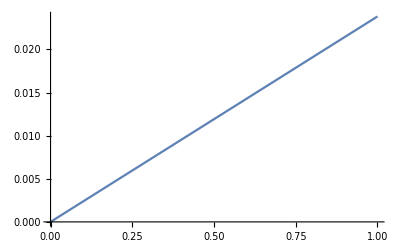

```mathematica
Plot[test1[x], {x, 1*^-5, 1.}]
```

```mathematica
analyticTT[ME_, DMmass_?NumericQ ] := Module[
{Ei, E0, Etherm},

Etherm = 3./2. TEMP;

E0 = 1.05*DMmass;
-1.*NIntegrate[1/test1[Ei], {Ei, E0, Etherm}]
];
```

```mathematica
analyticTT[constantME, 1.]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Ei$306649 near {Ei$306649} = {1.3500001664477024447107240459514068789599641117211829312305670925×10^-8}. NIntegrate obtained -1536.86 and 61.7186 for the integral and error estimates.

1536.86